We start out with the balance equations - total input to the queue (i.e. write rate, including copies) is A, and remaining traffic at the end of the queue is A-1:

```mathematica
eq1 = A * Exp[-α/A] == A-1
```

A ⅇ^(-α/A)==-1+A

```mathematica
eq2 = Map[(#/(-A))+1&,eq1]
```

1-ⅇ^(-α/A)==1-(-1+A)/A

```mathematica
eq3 = Simplify[Map[1/#&,eq2]]
```

1/(1-ⅇ^(-α/A))==A

With a change of variables, Mathematica is able to give us a solution:

```mathematica
eq4 = eq3/.{α/A->t,A->α/t}
```

1/(1-ⅇ^-t)==α/t

```mathematica
soln = Solve[eq4,t,InverseFunctions->True][[1]]
```

{t→α+ProductLog[-ⅇ^-α α]}

And now change back and we’ve solved for A, as seen in the graph below:

```mathematica
Subscript[A, lru][α_]=α/t/.soln
```

α/(α+W(-ⅇ^-α α))

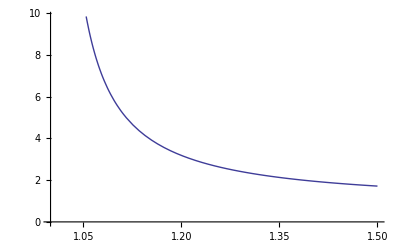

```mathematica
Plot[Subscript[A, lru][α],{α,1.03,1.5},AxesOrigin->{1,0}, PlotStyle-> Directive[Thick],TicksStyle->Directive[14]]
```